```mathematica
EulerForward[du_, du0_, t0_, T_, n_]:=Module[
{t, h, y, i, ret},

t=Subdivide[t0,T,n];
h = (T-t0)/n;

y= Table[0, Length[t]];

y[[1]] = du0;

For[i = 2, i≤ Length[t], i++,
y[[i]] = y[[i-1]]+h(du[y[[i-1]]]);
];

ret = Table[{t[[i]], y[[i]]}, {i,1,Length[t]}]
]
```

```mathematica
EulerBackwardsV1[du_,du0_, t0_, T_, n_]:=Module[
{t, h, y, i, ret, aprY},

aprY = EulerForward[du,du0, t0, T, n];

t=Subdivide[t0,T,n];
h = (T-t0)/n;

y= Table[0, Length[t]];
y[[1]] = du0;

For[i = 1, i≤ Length[t]-1, i++,
y[[i+1]] =fy/.FindRoot[fy == y[[i]]+h*du[fy], {fy, aprY[[i+1,2]]}]
];
ret = Table[{t[[i]], y[[i]]}, {i,1,Length[t]}]

]
```

```mathematica
f[u_]:=-10u;
```

```mathematica
NewtonSolve[f_, x0_, nmax_]:=Module[
{xprev, xcurr, i},
xprev = x0;

For[i=1, i≤nmax, i++,
xcurr = xprev-(f/.x->xprev)/(D[f, x]/.x->xprev);
If[Abs[xcurr-xprev]<10^6, 
Return[xcurr]];
xprev=xcurr;
];
xcurr
]
```

```mathematica
EulerBackwardsV2[du_,du0_, t0_, T_, n_]:=Module[
{t, h, y, i, ret, aprY},

aprY = EulerForward[du,du0, t0, T, n];

t=Subdivide[t0,T,n];
h = (T-t0)/n;

y= Table[0, Length[t]];
y[[1]] = du0;

For[i = 1, i≤ Length[t]-1, i++,
y[[i+1]]= NewtonSolve[y[[i]]+h*du[x]-x, aprY[[i+1,2]],10];

];
ret = Table[{t[[i]], y[[i]]}, {i,1,Length[t]}]
]
```

```mathematica
f[u_]:=10u(1-u);
```

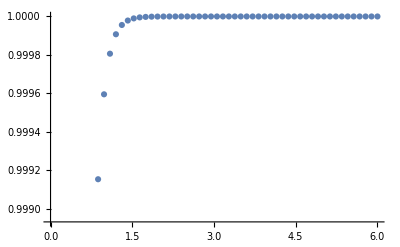

```mathematica
ListPlot[EulerBackwardsV2[f, 0.1, 0,6, 55]]
```